## 初识列表

列表是 Wolfram 语言中将对象集合在一起的一种基本方式。{1,2,3} 是一个数字列表。就其本身而言，列表不做任何事情；它们只是一种存储对象的方式。因此，如果你给定一个列表作为输入，它就会将列表原样返回。

```mathematica
{1,2,3,4,a,b,c}
```

{1,2,3,4,a,b,c}

ListPlot 是用于对数字列表进行绘图的函数。

绘制数字列表 {1,1,2,2,3,4,4}：

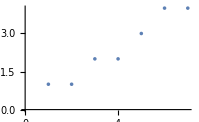

```mathematica
ListPlot[{1,1,2,2,3,4,4}]
```

绘制数字列表 {10,9,8,7,3,2,1}：

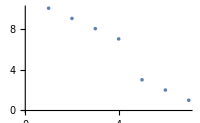

```mathematica
ListPlot[{10,9,8,7,3,2,1}]
```

Range 是用于创建数字列表的函数。

生成 10 以内的数字的列表：

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

生成一个数字列表，然后绘制它：

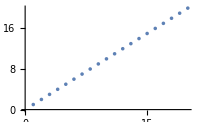

```mathematica
ListPlot[Range[20]]
```

Reverse 是将列表中的元素进行反转。

反转列表中的元素：

```mathematica
Reverse[{1,2,3,4}]
```

{4,3,2,1}

将 Range 生成的列表进行反转：

```mathematica
Reverse[Range[10]]
```

{10,9,8,7,6,5,4,3,2,1}

绘制反转后的列表：

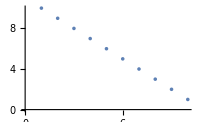

```mathematica
ListPlot[Reverse[Range[10]]]
```

Join 用于将列表连接在一起，生成一个单一的列表作为结果。

将列表连接在一起：

```mathematica
Join[{1,2,3},{4,5},{6,7}]
```

{1,2,3,4,5,6,7}

```mathematica
Join[{1,2,3},{1,2,3,4,5}]
```

{1,2,3,1,2,3,4,5}

连接两个由 Range 生成的列表：

```mathematica
Join[Range[3],Range[5]]
```

{1,2,3,1,2,3,4,5}

将连接后的三个列表绘制出来：

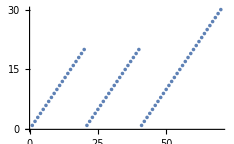

```mathematica
ListPlot[Join[Range[20],Range[20],Range[30]]]
```

反转中间的列表：

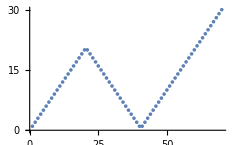

```mathematica
ListPlot[Join[Range[20],Reverse[Range[20]],Range[30]]]
```

词汇

{1,2,3,4} |   | 元素的列表
ListPlot[{1,2,3,4}] |   | 绘制一系列数字
Range[10] |   | 数字范围
Reverse[{1,2,3}] |   | 反转列表
Join[{4,5,6},{2,3,2}] |   | 将列表连接在一起

"共有 11 道习题"
"以及 5 道附加题" | "开始练习 »"

使用 Range 来创建列表 {1,2,3,4}。»

| 期望输出： |  
  | {1,2,3,4} |

创建 100 以内的数字的列表。»

| 期望输出： |  
  | {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100} |

使用 Range 和 Reverse 来创建{4,3,2,1}。»

| 期望输出： |  
  | {4,3,2,1} |

创建 1 到 50 的数字的倒序列表。»

| 期望输出： |  
  | {50,49,48,47,46,45,44,43,42,41,40,39,38,37,36,35,34,33,32,31,30,29,28,27,26,25,24,23,22,21,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1} |

使用 Range、Reverse 和 Join 来创建 {1,2,3,4,4,3,2,1}。»

| 期望输出： |  
  | {1,2,3,4,4,3,2,1} |

绘制一个列表，从 1 到 100，然后再降到 1。»

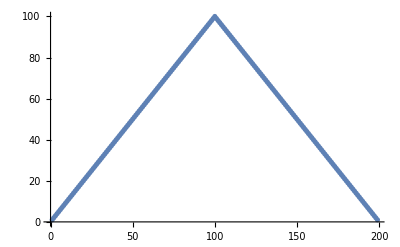
| 期望输出： |  
  | -Graphics- |

使用 Range 和 RandomInteger 来创建随机长度最长为 10 的列表。»

| 期望输出示例： |  
  | {1} |

为 Reverse[Reverse[Range[10]]] 找到一个更简单的形式。»

| 期望输出： |  
  | {1,2,3,4,5,6,7,8,9,10} |

为 Join[{1,2},Join[{3,4},{5}]] 找到一个更简单的形式。»

| 期望输出： |  
  | {1,2,3,4,5} |

为 Join[Range[10],Join[Range[10],Range[5]]] 找到一个更简单的形式。»

| 期望输出： |  
  | {1,2,3,4,5,6,7,8,9,10,1,2,3,4,5,6,7,8,9,10,1,2,3,4,5} |

为 Reverse[Join[Range[20],Reverse[Range[20]]]] 找到一个更简单的形式。»

| 期望输出： |  
  | {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1} |

计算 {1,2,3,4} 的反转的反转。»

| 期望输出： |  
  | {1,2,3,4} |

使用 Range、Reverse 和 Join 来创建列表 {1,2,3,4,5,4,3,2,1}。»

| 期望输出： |  
  | {1,2,3,4,5,4,3,2,1} |

使用 Range、Reverse 和 Join 来创建 {3,2,1,4,3,2,1,5,4,3,2,1}。»

| 期望输出： |  
  | {3,2,1,4,3,2,1,5,4,3,2,1} |

绘制数字列表 {10,11,12,13,14}。»

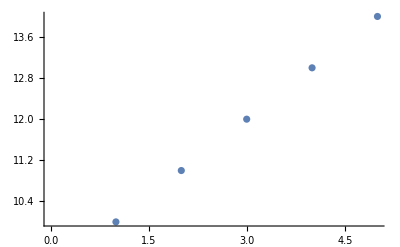
| 期望输出： |  
  | -Graphics- |

为 Join[Join[Range[10],Reverse[Range[10]]],Range[10]] 找到一个更简单的形式。»

| 期望输出： |  
  | {1,2,3,4,5,6,7,8,9,10,10,9,8,7,6,5,4,3,2,1,1,2,3,4,5,6,7,8,9,10} |

问&答

{1,2,3} 该怎样读出来？

通常读作“list 1 2 3”。“{” 和 “}” 称为“大括号”或“花括号”。“{” 是 “左括号”，“}” 是 “右括号”。

列表是一个函数吗？

是的，{1,2,3} 就是 List[1,2,3]。但与 Plus 不同的是，List 函数并不进行任何实际的计算；它只是原样返回。

ListPlot 绘制的是什么？

连续的列表元素的值。每个点的 x 值给出了其在列表中的位置；y 值为该元素的值。

列表可以有多长？

你想要多长都可以，直到你的电脑内存被耗尽为止。

技术笔记

Range[m,n] 将生成从 m 到 n 的数字列表。Range[m,n,s] 将生成从 m 到 n 的数字列表，步长为 s。

许多计算机语言都有类似列表(通常称为“数组”)的结构。但通常他们只允许包含明确的对象，比如数字；你不能创建一个像 {a,b,c} 这样的列表，你没有说 a、b 和 c 是什么。但在 Wolfram 语言中你可以，因为 Wolfram 语言是符号语言。

{a,b,c} 是一个有确定顺序的元素列表；{b,c,a} 是一个不同的列表。

像数学一样，你可以对 Wolfram 语言的函数提出定理。例如，Reverse[Reverse[x]] 等于 x。

探索更多

Wolfram 语言中的列表指南 »